## Halbach Array in Radia

```mathematica
(* Initialize Radia*)
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
(* Construct the segments of the circular Halbach Array *)
(* To do this, we need to create a segment outer radius R, inner radius R/2, which subtends an angle π/6. Thickness R. *)
(* In Radia, curves appear to be generated by taking convex polyhedra with many faces, which converges to a sphere at large numbers of faces. I attempt to do the same for an arc. *)
(* I will need to create a circular arc, then rotate it π/6 degrees, define the correct magnetization, translate and place it in the proper position. Repeat 12 times. *)
```

```mathematica
(* Create new Halbach array with spatially rotating magnetization *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
θ=π/12
dθ = π/2
(* outer radius *)
R = 25.4
halbach = radObjCnt[{}]

For[i=1, i< 13, i++,
(* set magnetization *)
mx = Cos[θ];
my =Sin[θ];
mz = 0;

Print["Magnetization angle for ", i," is: ", θ];

(* create segment geometry *)
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, -20}};
segment = Append[segment, {segment[[1]][[1]], 20}];
created = radObjMltExtPgn[segment, {mx, my, mz}];

(* iterate on variables *) 
φ += dφ;
θ+=dφ + dθ;

(* add to group *)
radObjAddToCnt[halbach, {created}];
]

(* color the object *)
radObjDrwAtr[halbach, {0, 0.5, 0.8}];

(* plot + show the object *)
RadPlot3DOptions[];
g = radObjDrw[halbach];
Show[Graphics3D[g]]
```

0

π/6

π/12

π/2

25.4

1

Magnetization angle for 1 is: π/12

Magnetization angle for 2 is: (3 π)/4

Magnetization angle for 3 is: (17 π)/12

Magnetization angle for 4 is: (25 π)/12

Magnetization angle for 5 is: (11 π)/4

Magnetization angle for 6 is: (41 π)/12

Magnetization angle for 7 is: (49 π)/12

Magnetization angle for 8 is: (19 π)/4

Magnetization angle for 9 is: (65 π)/12

Magnetization angle for 10 is: (73 π)/12

Magnetization angle for 11 is: (27 π)/4

Magnetization angle for 12 is: (89 π)/12

-Graphics3D-

```mathematica
(* Plot the y-component of the field strength to demonstrate spatial rotation *)
```

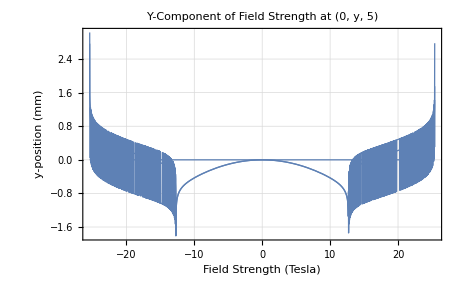

```mathematica
RadPlotOptions[];
Plot[radFld[halbach, "h", {0,y, 0}], {y, -R, R}, PlotLabel->"Y-Component of Field Strength at (0, y, 5)", AxesLabel->{"Field Strength (Tesla)", "y-position (mm)"}]
```

```mathematica
(* Plot the B-field *)
```

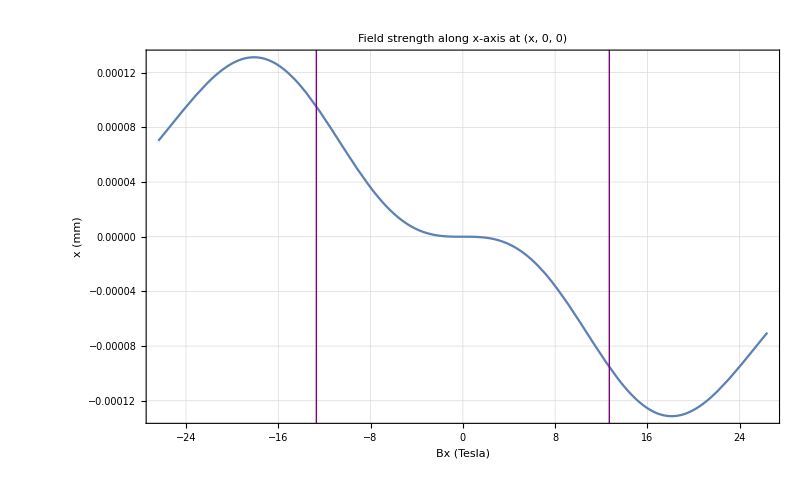

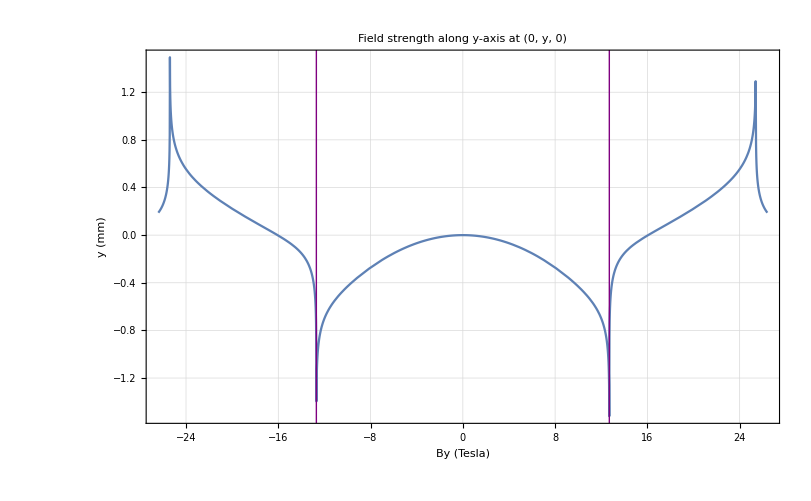

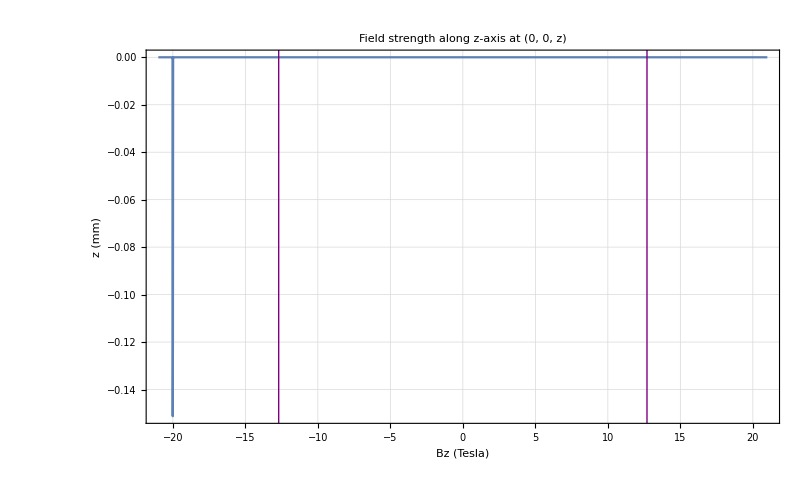

```mathematica
lineStyle={Thick,Purple};

(* draw lines at boundary of the inner radius *)
line1=Line[{{R/2,-10},{R/2,10}}];
line2=Line[{{-R/2,-10},{-R/2,10}}];

Plot[radFld[halbach, "hz", {x, 0, 0.1}], {x, -R -1, R + 1}, PlotLabel->"Field strength along x-axis at (x, 0, 0)", AxesLabel->{"Bx (Tesla)", "x (mm)"}, Epilog->{Directive[lineStyle], line1, line2}]

Plot[radFld[halbach, "hy", {0, y, 0.1}], {y, -R -1, R + 1}, PlotLabel->"Field strength along y-axis at (0, y, 0)", AxesLabel->{"By (Tesla)", "y (mm)"}, Epilog->{Directive[lineStyle], line1, line2}]

Plot[radFld[halbach, "hz", {0, 0, z}], {z, -20  - 1, 20 + 1}, PlotLabel->"Field strength along z-axis at (0, 0, z)", AxesLabel->{"Bz (Tesla)", "z (mm)"},Epilog->{Directive[lineStyle], Line[{{-R/2, -10}, {-R/2, 10}}], Line[{{R/2, -10}, {R/2, 10}}]}]
```

```mathematica
(* Plot the norm of the B-field *)
```

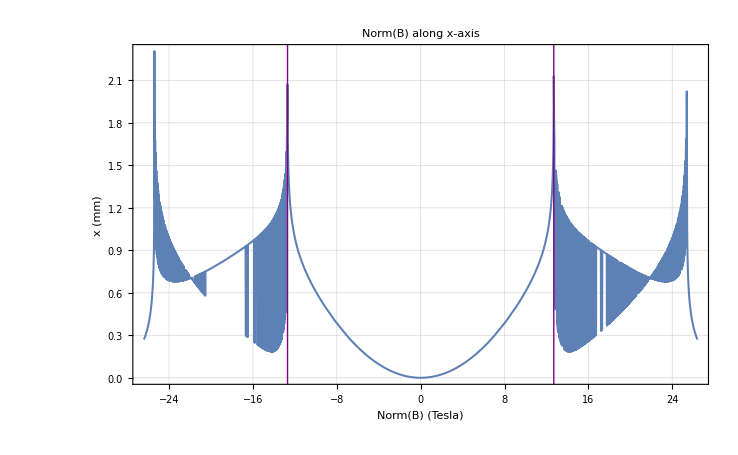

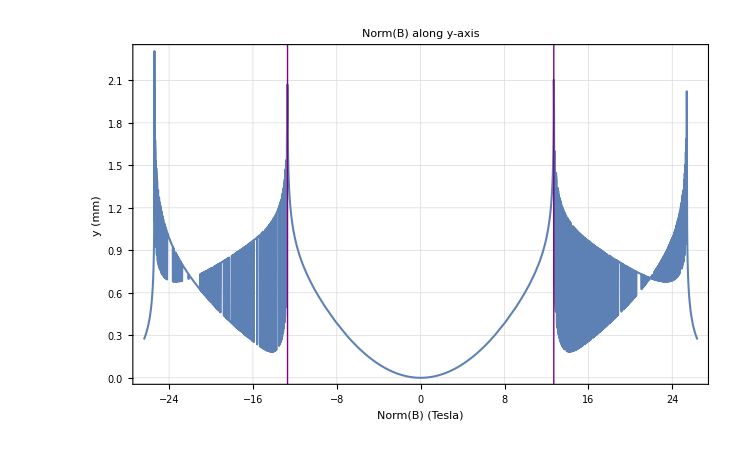

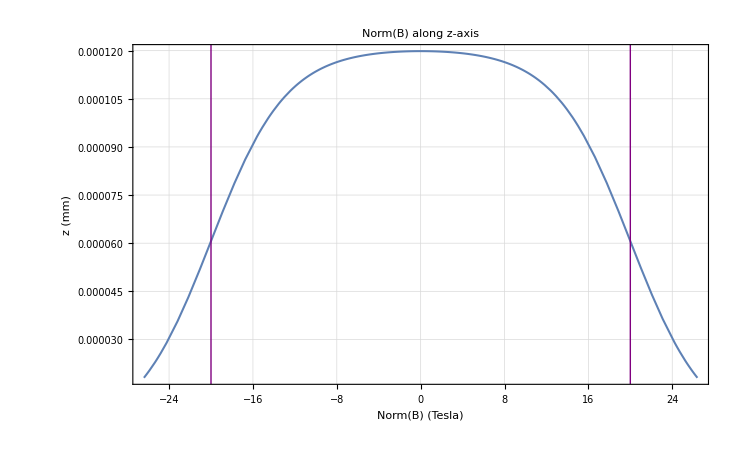

```mathematica
(* define norm function *)
norm [x_, y_, z_]:= Module[{bx, by, bz}, 
bx = radFld[halbach, "hx", {x, y, z}];
by = radFld[halbach, "hy", {x, y, z}];
bz = radFld[halbach, "hz", {x, y, z}];
Return[Sqrt[bx^2 + by^2 + bz^2]];
]

lineStyle={Thick,Purple};
line1=Line[{{R/2,-10},{R/2,10}}];
line2=Line[{{-R/2,-10},{-R/2,10}}];

Plot[norm[x, 0, 0], {x, -R-1, R+1}, PlotLabel->"Norm(B) along x-axis", AxesLabel->{"Norm(B) (Tesla)", "x (mm)"},Epilog->{Directive[lineStyle],line1,line2}]

Plot[norm[0, y, 0], {y,-R-1, R+1}, PlotLabel->"Norm(B) along y-axis", AxesLabel->{"Norm(B) (Tesla)", "y (mm)"},Epilog->{Directive[lineStyle],line1,line2}]

Plot[norm[0.1, 0.1, z], {z, -R - 1, R+ 1}, PlotLabel->"Norm(B) along z-axis", AxesLabel->{"Norm(B) (Tesla)", "z (mm)"},Epilog->{Directive[lineStyle],Line[{{-20,-10},{-20,10}}],Line[{{20,-10},{20,10}}]}]
```

```mathematica
(* Make a matrix of the B-field values for use with Python, export to a .csv file *)
```

```mathematica
(* initialize variables *)
xStart = -R;
yStart = -R;
zStart = -R/2;
n =4;
bxMatrix = {};
byMatrix = {};
bzMatrix = {};
normbMatrix = {};

(* iterate through points on x, y, z axes *)
For[i=1, i≤ n, i++, 
bxMatrix=Append[bxMatrix, {}];
For[j=1, j≤ n, j++,
bxMatrix[[i]]=Append[bxMatrix[[i]], {}];
For[k=1,k≤ n, k++,
bxMatrix[[i]][[j]]=Append[bxMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number n to get the step size, and iterate over the steps *)
radFld[halbach, "Bx", {xStart + (2*R)/(n-1)*(i-1), yStart + (2*R)/(n-1)*(j-1), zStart+ R/(n-1)*(k-1)}]];
];
];
];

For[i=1, i≤ n, i++, 
byMatrix=Append[byMatrix, {}];
For[j=1, j≤ n, j++,
byMatrix[[i]]=Append[byMatrix[[i]], {}];
For[k=1,k≤ n, k++,
byMatrix[[i]][[j]]=Append[byMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number n to get the step size, and iterate over the steps *)
radFld[halbach, "By", {xStart + (2*R)/(n-1)*(i-1), yStart + (2*R)/(n-1)*(j-1), zStart+ R/(n-1)*(k-1)}]];
];
];
];

For[i=1, i≤ n, i++, 
bzMatrix=Append[bzMatrix, {}];
For[j=1, j≤ n, j++,
bzMatrix[[i]]=Append[bzMatrix[[i]], {}];
For[k=1,k≤ n, k++,
bzMatrix[[i]][[j]]=Append[bzMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number n to get the step size, and iterate over the steps *)
radFld[halbach, "Bz", {xStart + (2*R)/(n-1)*(i-1), yStart + (2*R)/(n-1)*(j-1), zStart+ R/(n-1)*(k-1)}]];
];
];
];

For[i=1, i≤ n, i++, 
normbMatrix=Append[normbMatrix, {}];
For[j=1, j≤ n, j++,
normbMatrix[[i]]=Append[normbMatrix[[i]], {}];
For[k=1,k≤ n, k++,
normbMatrix[[i]][[j]]=Append[normbMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number n to get the step size, and iterate over the steps *)
norm[xStart + (2*R)/(n-1)*(i-1), yStart + (2*R)/(n-1)*(j-1), zStart+ R/(n-1)*(k-1)]]
];
];
];

Print["bxMatrix: ", MatrixForm[bxMatrix]]
Print["byMatrix: ", MatrixForm[byMatrix]]
Print["bzMatrix: ", MatrixForm[bzMatrix]]
Print["normbMatrix: ", MatrixForm[normbMatrix]]


SetDirectory["/Users/andrewwinnicki/Desktop/andrew/2019-2020/Doyle Lab/Modeling Project/B-Matrix"];
Export["bxMatrix.fits",bxMatrix];
Export["byMatrix.fits",byMatrix];
Export["bzMatrix.fits",bzMatrix];
Export["normbMatrix.fits",normbMatrix];
```

bxMatrix: ((0.00355379
0.0041655
0.0041655
0.00355379) | (0.115136
0.0987448
0.0987448
0.115136) | (0.0778662
0.0853362
0.0853362
0.0778662) | (-0.00763981
-0.00738911
-0.00738911
-0.00763981)
(-0.0934892
-0.0899161
-0.0899161
-0.0934892) | (0.525447
0.561992
0.561992
0.525447) | (-0.545323
-0.564361
-0.564361
-0.545323) | (-0.079963
-0.089947
-0.089947
-0.079963)
(-0.079963
-0.089947
-0.089947
-0.079963) | (-0.545323
-0.564361
-0.564361
-0.545323) | (0.525447
0.561992
0.561992
0.525447) | (-0.0934892
-0.0899161
-0.0899161
-0.0934892)
(-0.00763981
-0.00738911
-0.00738911
-0.00763981) | (0.0778662
0.0853362
0.0853362
0.0778662) | (0.115136
0.0987448
0.0987448
0.115136) | (0.00355379
0.0041655
0.0041655
0.00355379))

byMatrix: ((-0.00355379
-0.0041655
-0.0041655
-0.00355379) | (0.0934892
0.0899161
0.0899161
0.0934892) | (0.079963
0.089947
0.089947
0.079963) | (0.00763981
0.00738911
0.00738911
0.00763981)
(-0.115136
-0.0987448
-0.0987448
-0.115136) | (-0.525447
-0.561992
-0.561992
-0.525447) | (0.545323
0.564361
0.564361
0.545323) | (-0.0778662
-0.0853362
-0.0853362
-0.0778662)
(-0.0778662
-0.0853362
-0.0853362
-0.0778662) | (0.545323
0.564361
0.564361
0.545323) | (-0.525447
-0.561992
-0.561992
-0.525447) | (-0.115136
-0.0987448
-0.0987448
-0.115136)
(0.00763981
0.00738911
0.00738911
0.00763981) | (0.079963
0.089947
0.089947
0.079963) | (0.0934892
0.0899161
0.0899161
0.0934892) | (-0.00355379
-0.0041655
-0.0041655
-0.00355379))

bzMatrix: ((3.27402×10^-12
4.1588×10^-12
6.43565×10^-12
6.6766×10^-12) | (-0.00288303
-0.00357606
0.00357606
0.00288303) | (0.00481164
0.000836163
-0.000836163
-0.00481164) | (-0.00231628
0.000132453
-0.000132453
0.00231628)
(0.00288303
0.00357606
-0.00357606
-0.00288303) | (-3.96447×10^-11
-1.01425×10^-11
-8.65656×10^-12
-5.06787×10^-11) | (0.0591336
0.00612958
-0.00612958
-0.0591336) | (0.00481164
0.000836163
-0.000836163
-0.00481164)
(-0.00481164
-0.000836163
0.000836163
0.00481164) | (-0.0591336
-0.00612958
0.00612958
0.0591336) | (-9.68392×10^-14
-2.29769×10^-12
-8.63632×10^-12
-1.30349×10^-11) | (-0.00288303
-0.00357606
0.00357606
0.00288303)
(0.00231628
-0.000132453
0.000132453
-0.00231628) | (-0.00481164
-0.000836163
0.000836163
0.00481164) | (0.00288303
0.00357606
-0.00357606
-0.00288303) | (-3.22664×10^-12
-3.97776×10^-12
-4.10191×10^-12
-2.7104×10^-12))

normbMatrix: ((0.00502581
0.00589091
0.00589091
0.00502581) | (0.14834
0.133597
0.133597
0.14834) | (0.111716
0.12399
0.12399
0.111716) | (0.0110498
0.0104506
0.0104506
0.0110498)
(0.14834
0.133597
0.133597
0.14834) | (0.743095
0.794777
0.794777
0.743095) | (0.773466
0.798151
0.798151
0.773466) | (0.111716
0.12399
0.12399
0.111716)
(0.111716
0.12399
0.12399
0.111716) | (0.773466
0.798151
0.798151
0.773466) | (0.743095
0.794777
0.794777
0.743095) | (0.14834
0.133597
0.133597
0.14834)
(0.0110498
0.0104506
0.0104506
0.0110498) | (0.111716
0.12399
0.12399
0.111716) | (0.14834
0.133597
0.133597
0.14834) | (0.00502581
0.00589091
0.00589091
0.00502581))